#### Zad. 1

-48-24 x+24 x^2+12 x^3

{{x→-2},{x→-√2},{x→√2}}

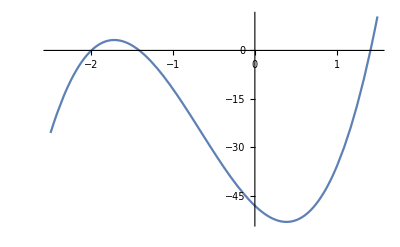

3 x^4+8 x^3-12 x^2-48 x+5

```mathematica
y=-48 x-12 x^2+8 x^3+3 x^4+5;
D[y,x]
Solve[%==0,x]
Plot[%%,{x,-2.5,1.5}]
y//TeXForm
```

#### Zad. 2

```mathematica
Integrate[4/x^3-3/Sin[x]^2+5/((x^2)^(1/3)),x]
Integrate[x^2 Exp[3-2 x^3],x]
Integrate[x^4 Log[x],x]
```

-2/x^2+(15 x)/((x^2)^(1/3))+3 Cot[x]

-1/6 ⅇ^(3-2 x^3)

-x^5/25+1/5 x^5 Log[x]

#### Zad. 3

```mathematica
2/x-3/x^2+1/(x+1)//Together;
Expand[Numerator[%]]/Expand[Denominator[%]]
Integrate[%,x]
```

(-3-x+3 x^2)/(x^2+x^3)

3/x+2 Log[x]+Log[1+x]